```mathematica
ClearAll["Global`*"];
(*データの読み込み*)
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"mathematica_plot_options.nb"}]];
expData=Import[FileNameJoin[{NotebookDirectory[],"exp.csv"}],"Data"];
simuData=Import[FileNameJoin[{NotebookDirectory[],"analysis_1.csv"}],"Data"];
```

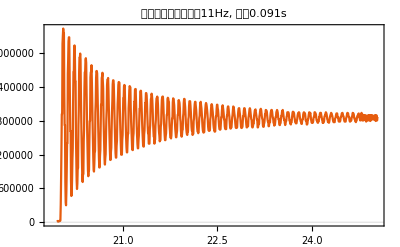

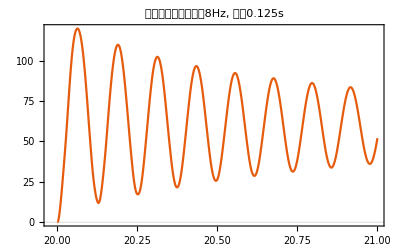

```mathematica
(*適当な範囲を抜き出す．プロット*)
expData=expData[[110;;-10]];
simuData=simuData[[3900;;]];
ListPlot[expData,Joined->True,PlotRange->All,Evaluate[plot2Doption],PlotLabel->"元データ．約振動数11Hz,　周期0.091s"]
ListPlot[simuData,Joined->True,Evaluate[plot2Doption],PlotLabel->"元データ．約振動数8Hz,　周期0.125s"]
```

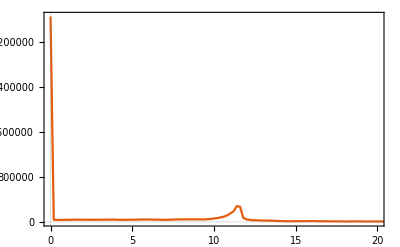

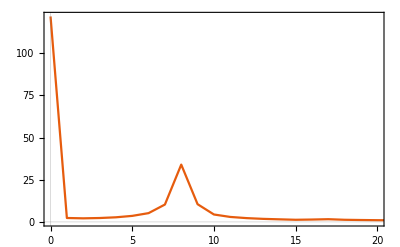

```mathematica
(*あらかじめ作った，mathematica_plot_options.nb内にある，interpolateAndFourierでフーリエ解析*)
{expTime,expDisp}=Transpose[expData];
{simuTime,simuDisp}=Transpose[simuData];

ListPlot[interpolateAndFourier[expTime,expDisp],PlotRange->{{0,20},All},Joined->True,Evaluate[plot2Doption]]
ListPlot[interpolateAndFourier[simuTime,simuDisp],PlotRange->{{0,20},All},Joined->True,Evaluate[plot2Doption]]
```

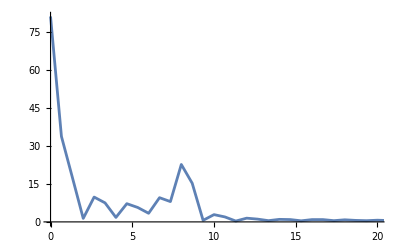

-Graphics-

```mathematica
(*先生の結果．解析結果のフーリエだろう*)
ListPlot[Import[FileNameJoin[{NotebookDirectory[],"fourier_exp.csv"}],"Data"],PlotRange->{{0,20},All},Joined->True]
ListPlot[Import[FileNameJoin[{NotebookDirectory[],"fourier_ana_1.csv"}],"Data"],PlotRange->{{0,20},All},Joined->True]
```